```mathematica
$Assumptions=q>0&&q<1 &&v>0 &&x<1/q&&a>0&&b>0&&y<x
```

q>0&&q<1&&v>0&&x<1/q&&a>0&&b>0&&y<x

```mathematica
λ=FullSimplify[(a(1-q x))/((1-q x)^2+q^2 y^2)-(b((1-q x)^2-q^2 y^2))/(((1-q x)^2+q^2 y^2)^2)-x(1/(x^2+y^2)-(a q)/((1-q x)^2+q^2 y^2)+(2b q (1-q x))/(((1-q x)^2+q^2 y^2)^2))+x/(x^2+y^2)]
```

((-1+q x) (-a+b+(a+b) q x)+(a+b) q^2 y^2)/(((-1+q x)^2+q^2 y^2)^2)

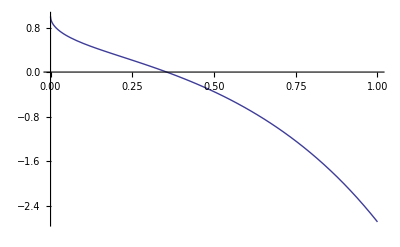

```mathematica
Plot[1-1/2 ⅇ^(2u)Erf[√(8u)],{u,0, 1}]
```

```mathematica
f[x_,v_,q_]=((Erf[√(2v)]-1+1/2 ⅇ^(2v)Erf[√(8v)])-((Erf[√(2v)]+1-1/2 ⅇ^(2v)Erf[√(8v)])q x))/(1-q x)^3
```

(-1+Erf[√2 √v]+1/2 ⅇ^(2 v) Erf[2 √2 √v]-q x (1+Erf[√2 √v]-1/2 ⅇ^(2 v) Erf[2 √2 √v]))/(1-q x)^3

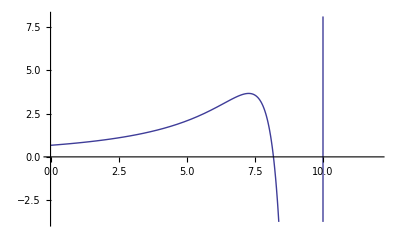

```mathematica
Plot[f[x,0.32,0.1],{x,0,12}]
```

```mathematica
Clear[λ]
```

```mathematica
Solve[λ==((a-b)-(a+b)q x)/(1-q x)^3,x]
```

```mathematica
{{x->1/q-(2^(1/3) (-3 a q^4 λ-3 b q^4 λ))/(3 q^3 λ (54 b q^6 λ^2+√(2916 b^2 q^12 λ^4+4 (-3 a q^4 λ-3 b q^4 λ)^3))^(1/3))+((54 b q^6 λ^2+√(2916 b^2 q^12 λ^4+4 (-3 a q^4 λ-3 b q^4 λ)^3))^(1/3))/(3 2^(1/3) q^3 λ)},{x->1/q+((1+ⅈ √3) (-3 a q^4 λ-3 b q^4 λ))/(3 2^(2/3) q^3 λ (54 b q^6 λ^2+√(2916 b^2 q^12 λ^4+4 (-3 a q^4 λ-3 b q^4 λ)^3))^(1/3))-((1-ⅈ √3) (54 b q^6 λ^2+√(2916 b^2 q^12 λ^4+4 (-3 a q^4 λ-3 b q^4 λ)^3))^(1/3))/(6 2^(1/3) q^3 λ)},{x->1/q+((1-ⅈ √3) (-3 a q^4 λ-3 b q^4 λ))/(3 2^(2/3) q^3 λ (54 b q^6 λ^2+√(2916 b^2 q^12 λ^4+4 (-3 a q^4 λ-3 b q^4 λ)^3))^(1/3))-((1+ⅈ √3) (54 b q^6 λ^2+√(2916 b^2 q^12 λ^4+4 (-3 a q^4 λ-3 b q^4 λ)^3))^(1/3))/(6 2^(1/3) q^3 λ)}}
```

```mathematica
Information[q]
```

Global`q

```mathematica
Information[ξ]
```

Global`ξ

```mathematica
Assuming[ξ>0,Solve[q-1/2==(a(ξ-b/a)^2+a q^2 w-b^2/a)/((ξ^2+q^2 w)^2),w]]
```

{{w→(a q^2+q^2 ξ^2-2 q^3 ξ^2-√(a^2 q^4+4 b q^4 ξ-8 b q^5 ξ))/(-q^4+2 q^5)},{w→(a q^2+q^2 ξ^2-2 q^3 ξ^2+√(a^2 q^4+4 b q^4 ξ-8 b q^5 ξ))/(-q^4+2 q^5)}}

```mathematica
Simplify[Replace[(a q^2+q^2 ξ^2-2 q^3 ξ^2+√(a^2 q^4+4 b q^4 ξ-8 b q^5 ξ))/(-q^4+2 q^5),ξ-> q((2^(1/3) (-3 a q^4 λ-3 b q^4 λ))/(3 q^3 λ (54 b q^6 λ^2+√(2916 b^2 q^12 λ^4+4 (-3 a q^4 λ-3 b q^4 λ)^3))^(1/3))+((54 b q^6 λ^2+√(2916 b^2 q^12 λ^4+4 (-3 a q^4 λ-3 b q^4 λ)^3))^(1/3))/(3 2^(1/3) q^3 λ)),∞]]
```

1/(9 q^4 (-1+2 q))(9 a q^2+(q^2 (3^(1/3) a λ+3^(1/3) b λ-(9 b λ^2+√3 √(-λ^3 (a^3+3 a^2 b+3 a b^2+b^3-27 b^2 λ)))^(2/3))^2)/(λ^2 (3 b λ^2+(√(-λ^3 (a^3+3 a^2 b+3 a b^2+b^3-27 b^2 λ)))/(√3))^(2/3))-(2 q^3 (3^(1/3) a λ+3^(1/3) b λ-(9 b λ^2+√3 √(-λ^3 (a^3+3 a^2 b+3 a b^2+b^3-27 b^2 λ)))^(2/3))^2)/(λ^2 (3 b λ^2+(√(-λ^3 (a^3+3 a^2 b+3 a b^2+b^3-27 b^2 λ)))/(√3))^(2/3))+3 √3 √((q^4 (4 3^(2/3) a b (-1+2 q) λ+3 a^2 λ (9 b λ^2+√3 √(-λ^3 (a^3+3 a^2 b+3 a b^2+b^3-27 b^2 λ)))^(1/3)+4 3^(1/3) b (-1+2 q) (3^(1/3) b λ-(9 b λ^2+√3 √(-λ^3 (a^3+3 a^2 b+3 a b^2+b^3-27 b^2 λ)))^(2/3))))/(λ (9 b λ^2+√3 √(-λ^3 (a^3+3 a^2 b+3 a b^2+b^3-27 b^2 λ)))^(1/3))))

```mathematica
Information[λ]
```

Global`λ

```mathematica
Solve[λ==(a-b-(a+b)(u-1))/u^3,u]
```

{{u→-(2^(1/3) (a+b))/((54 a λ^2+√(108 (a+b)^3 λ^3+2916 a^2 λ^4))^(1/3))+((54 a λ^2+√(108 (a+b)^3 λ^3+2916 a^2 λ^4))^(1/3))/(3 2^(1/3) λ)},{u→((1+ⅈ √3) (a+b))/(2^(2/3) (54 a λ^2+√(108 (a+b)^3 λ^3+2916 a^2 λ^4))^(1/3))-((1-ⅈ √3) (54 a λ^2+√(108 (a+b)^3 λ^3+2916 a^2 λ^4))^(1/3))/(6 2^(1/3) λ)},{u→((1-ⅈ √3) (a+b))/(2^(2/3) (54 a λ^2+√(108 (a+b)^3 λ^3+2916 a^2 λ^4))^(1/3))-((1+ⅈ √3) (54 a λ^2+√(108 (a+b)^3 λ^3+2916 a^2 λ^4))^(1/3))/(6 2^(1/3) λ)}}